## Handmade Expression Trees

x + 2 y

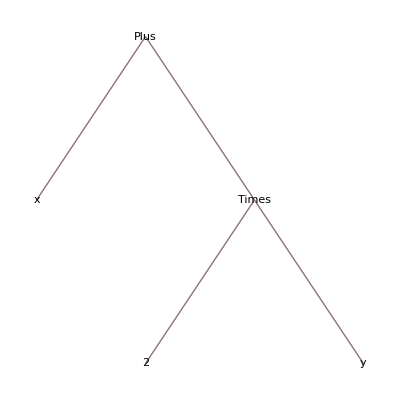

```mathematica
x+2y//TreeForm
```

```mathematica
Remove[op]
```

```mathematica
op[x_,loc_]:=Text[Style[x,Bold,Large,FontFamily->"Courier"],loc]
```

```mathematica
op["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
edge[op1_,op2_,sf_]:=Arrow[{op1,op2},Scaled[sf]]
```

```mathematica
spd=.0005
```

0.0005

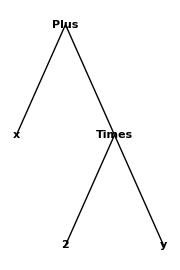

```mathematica
Show[
Graphics[
{
Arrowheads[0],
op["x",{0,1}],
op["Plus",{1,2}],
op["2",{1,0}],
op["y",{3,0}],
op["Times",{2,1}],
edge[{1,2},{0,1},spd],
edge[{1,2},{2,1},spd],
edge[{2,1},{1,0},spd],
edge[{2,1},{3,0},spd]},
Background->White,ImageSize->Small, AspectRatio->3/2
]
]
```

```mathematica
jump=1; mid=1.5;
```

```mathematica
Manipulate[jump=1; mid=1.5;
xloc={mid-1.5 jump,2-d};
plusloc={mid-.5jump-.5(1-d) ,2};
twoloc={mid-.5 jump-.05(1-d),2-2d};timesloc={mid+.5jump-.7(1-d),2-d};
yloc={mid+1.5jump-1.3(1-d),2-2d};
spc=.0007 +.0006(1-d);
Show[
Graphics[
{
Arrowheads[0],
op["x",xloc],
op["+",plusloc],
op["2",twoloc],
op["*",timesloc],
op["y",yloc],
edge[plusloc,xloc,spc],
edge[plusloc,timesloc,spc+.0002(1-d)],
edge[timesloc,twoloc,spc],
edge[timesloc,yloc,spc]
},
Background->White,ImageSize->Small, AspectRatio->2
],
PlotRange->{{-.2,3.2},{-.2,2.2}}
],
{d,0,1}, SaveDefinitions->True
]
```

(x + 2) y

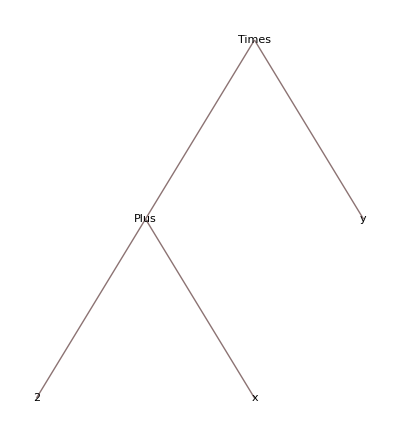

```mathematica
(x+2)y//TreeForm
```

```mathematica
Manipulate[jump=1; mid=2.0;
lploc={mid-1.5jump-.4,2};
rploc={mid-.5 jump+.4,2};
xloc={mid-1.5 jump,2-2d};
plusloc={mid-.5jump-.5(1-d) ,2-d};
twoloc={mid+.5 jump-(1-d),2-2d};timesloc={mid+.9jump-.7(1-d),2};
yloc={mid+2jump-1.3(1-d),2-d};
spc=.0007 +.0006(1-d);
Show[
Graphics[
{
Arrowheads[0],
GrayLevel[Min[1,3d]],
op["(",lploc],
op[")",rploc],
Black,
op["x",xloc],
op["+",plusloc],
op["2",twoloc],
op["*",timesloc],
op["y",yloc],
edge[plusloc,xloc,spc+.0004(1-d)],
edge[plusloc,twoloc,spc],
edge[timesloc,yloc,spc],
edge[timesloc,plusloc,spc+.0008(1-d)]
},
Background->White,ImageSize->Small, AspectRatio->2
],
PlotRange->{{-.2,4.2},{-.2,2.2}}
],
{d,0,1},SaveDefinitions->True
]
```